# Section 4 Excercise 4.2

```mathematica
Clear[f,f1,f2,euler,Heun,RK,euler,eulergraph,Heungraph,RKgraph,eug,heg,rug,ext]
```

## Excercise 4.2(1)

```mathematica
f[x_,t_]:=-Sin[x];
f1[x1_,x2_,t_]:= x2;
f2[x1_,x2_,t_]:= -Sin[x1];
```

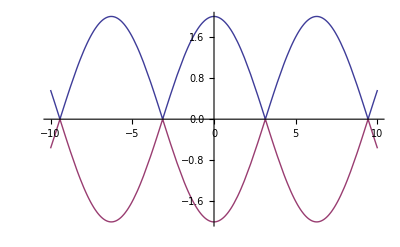
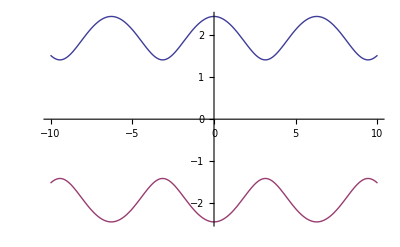
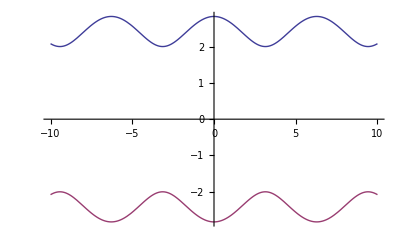
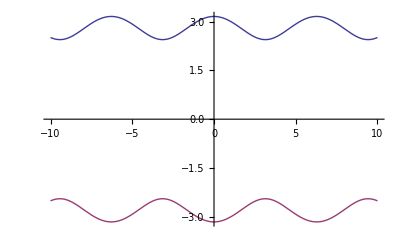
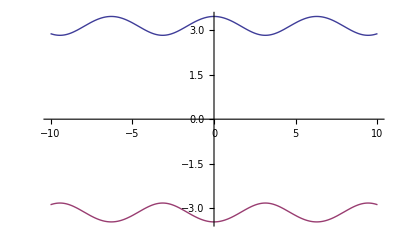

```mathematica
f[C_]:=Plot[{√(2(C+Cos[x])),-√(2(C+Cos[x]))},{x,-10,10}]
Table[f[c],{c,1,5}]
```

## Excercise 4.2(2)

## Euler Method

```mathematica
euler::nonnegativeint = "Nmax must be a non-negative integer";

euler[dt_,Nmax_,a1_,a2_]:= Module[{j = 0,n,x1,x2,t},If[Or[Nmax≤ 0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],x1[0]:=a1;x2[0]:= a2;x1[j_]:=(x1[j] = x1[j-1]+dt f1[x1[j-1],x2[j-1],t]);x2[j_] := (x2[j] = x2[j-1]+dt f2[x1[j-1],x2[j-1],t]);Table[{x1[j],x2[j]},{j,0,Nmax}]
]];
```

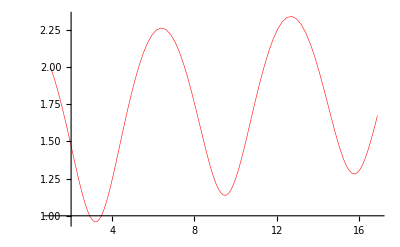

```mathematica
eulergraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[euler[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[1,0,0]},PlotRange->All];
eulergraph[.1,100,1,2]
```

## Heun Method

```mathematica
Heun[dt_,Nmax_,a1_,a2_]:= Module[{j = 0,n,g1,g2,h1,h2,x1,x2,t},If[Or[Nmax≤ 0,Not[IntegerQ[Nmax]]],Message[Heun::nonnegativeint],x1[0]:=a1;x2[0]:= a2;
g1[j_]:=(g1[j]=f1[x1[j],x2[j],t]);
h1[j_]:=(h1[j]=f2[x1[j],x2[j],t]);

g2[j_]:=(g2[j]=f1[x1[j]+dt g1[j],x2[j]+dt h1[j],t+dt]);
h2[j_]:=(h2[j]=f2[x1[j]+dt g1[j],x2[j]+dt h1[j],t+dt]);
x1[j_] := (x1[j] =x1[j-1]+ dt/2(g1[j-1] +g2[j-1]));
x2[j_] := (x2[j] = x2[j-1]+dt/2(h1[j-1] + h2[j-1]));
Table[{x1[j],x2[j]},{j,0,Nmax}]
]
];
```

```mathematica
Heungraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[Heun[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[0,1,0]},PlotRange->All];
```

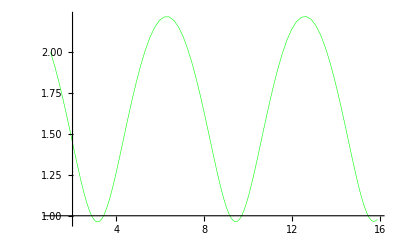

```mathematica
Heungraph[0.1,100,1,2]
```

## Runge Kutta Method

```mathematica
RK::nonnegativeint = "Nmax must be a non-negative integer";

RK[dt_,Nmax_,a1_,a2_]:= Module[{j = 0,n,g1,g2,g3,g4,h1,h2,h3,h4,x1,x2,t},If[Or[Nmax≤ 0,Not[IntegerQ[Nmax]]],Message[RK::nonnegativeint],
x1[0]:=a1;x2[0]:= a2;
g1[j_]:=(g1[j] =f1[x1[j],x2[j],t]);
h1[j_]:=(h1[j]=f2[x1[j],x2[j],t]);

g2[j_]:=(g2[j] =f1[x1[j]+dt/2  g1[j],x2[j]+dt/2  h1[j],t+dt/2]);
h2[j_]:=(h2[j]=f2[x1[j]+dt /2  g1[j],x2[j]+dt/2  h1[j],t+dt/2]);

g3[j_]:=(g3[j] =f1[x1[j]+dt/2  g2[j],x2[j] +dt/2 h2[j],t +dt/2]);
h3[j_]:=(h3[j]=f2[x1[j]+dt /2  g2[j],x2[j]+dt/2  h2[j],t +dt/2]);

g4[j_]:=(g4[j] =f1[x1[j]+dt g3[j] ,x2[j] +dt h3[j],t+dt]);
h4[j_]:=(h4[j]=f2[x1[j]+dt  g3[j] ,x2[j] +dt h3[j],t+dt]);
x1[j_] := (x1[j] =x1[j-1]+ dt/6(g1[j-1] +2g2[j-1]+2g3[j-1]+g4[j-1]));
x2[j_] := (x2[j] = x2[j-1]+dt/6(h1[j-1] + 2h2[j-1]+2h3[j-1]+h4[j-1]));
Table[{x1[j],x2[j]},{j,0,Nmax}]
]
];
```

```mathematica
RKgraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[RK[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[0,0,1]},PlotRange->All];
```

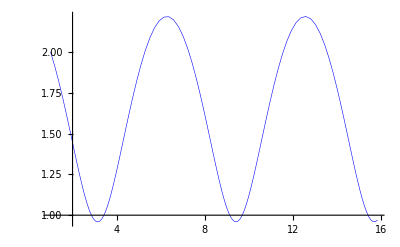

```mathematica
RKgraph[0.1,100,1,2]
```

## Analytic

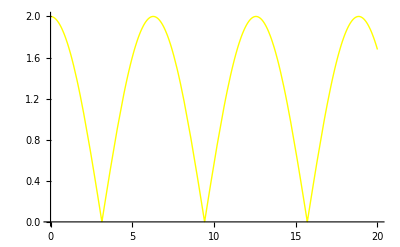

```mathematica
asol[a1_,a2_] := DSolve[{x''[t] == f[x[t],t],x[0] == a1,x'[0] == a2},x[t],t];
agraph[a1_,a2_,tlast_]:= Plot[Evaluate[x[t]/.asol[a1,a2]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,0,1]},PlotRange->All];
exactgraph[dt_,Nmax_,a1_,a2_]:=Plot[√(2+2 Cos[t]),{t,0,dt*Nmax},PlotStyle->RGBColor[1,1,0]];
exactgraph[0.1,200,1,2]
```

## Comparison of Approximation for 3 methods

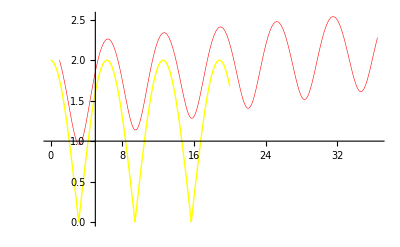

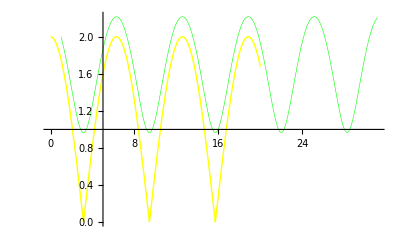

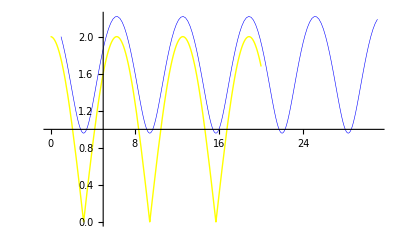

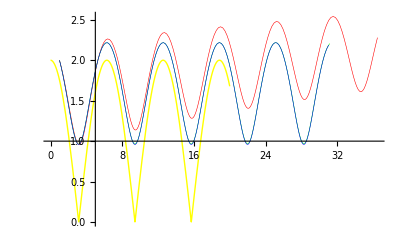

```mathematica
eug=eulergraph[.1,200,1,2];
heg=  Heungraph[.1,200,1,2];
rug=RKgraph[.1,200,1,2];
ext=exactgraph[.1,200,1,2];
Show[eug,ext]   
Show[heg,ext]
Show[rug,ext]
Show[eug,heg,rug,ext]
```

```mathematica
Red : Euler、Green : Heun, light Green : Runge Kutta、Yellow:analytic
```

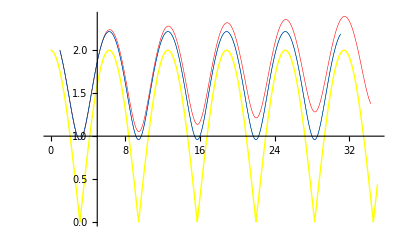

```mathematica
eug=eulergraph[.05,400,1,2];
heg=  Heungraph[.05,400,1,2];
rug=RKgraph[.05,400,1,2];
ext=exactgraph[.05,700,1,2];
Show[eug,heg,rug,ext]
```

Heun Method Graph and Runge  Kutta Graph already superposed with one another. Euler Method has still bad approximation.

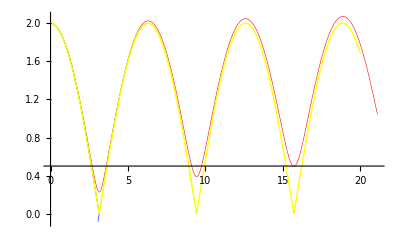

```mathematica
eug=eulergraph[.02,1000,0,2];
heg=  Heungraph[.02,1000,0,2];
rug=RKgraph[.02,1000,0,2];
ext=exactgraph[.02,1000,0,2];
Show[eug,heg,rug,ext]
```

Euler Method is very slow to approximate.In our problem Heun and Runge -Kutta are showing same level of approximation.